## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: DoublePendulumNEW.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/mikel/1-Artikulua-Esperimentuak-4B/15-EsperimentuaV154 (artikulua)/Packages/

```mathematica
Get["DoublePendulumNEW`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Orange;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleHairer=Yellow;
StyleError=Lighter[Blue,.6];
StyleEstimation=Orange;
StyleHamT12=Directive[Dashed,Red];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

### Paths

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

### Input Files

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileB=NotebookDirectory[]<>DataDirectory<>"outB.bin";
fileC=NotebookDirectory[]<>DataDirectory<>"outC.bin";
fileD=NotebookDirectory[]<>DataDirectory<>"outD.bin";
fileE=NotebookDirectory[]<>DataDirectory<>"outE.txt";
```

### Output Files

```mathematica
esperiment="CDP";
(* energy error*)
plot1=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3A.pdf";
plot1b=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3B.pdf";
plot2=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot2.pdf";
plot11=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot11.pdf";
plot12=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot12.pdf";
plot13=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot13.pdf";
(*Global errors*)
plot3=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"4A.pdf";
plot3b=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"4B.pdf";
(* distribution of energy jumps*)
plot4=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"2A.pdf";
plot5=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"2B.pdf";
plot5D=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot5D.pdf";
(* error estimation*)
plot6=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"5B.pdf";
plot6a=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"5A.pdf"; 
plot7=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot7.pdf";
```

## Parameters (CDP -NEW- initial values)

### Problem parameters and initial values.

```mathematica
prec=100;
n=2;
g=98/10;
m1=1;m2=1;
l1=1;l2=1;

C1=-l1^2 (m1+m2);
C2=-l2^2 m2;
C3=-2 l1 l2 m2 ;
C4=-2 l1^2 l2^2 m1 m2-l1^2 l2^2 m2^2;
C5=-l1^2 l2^2 m2^2;
C6=g l1 (m1+m2);
C7= g l2 m2;

Q10=0;
Q20=0;
P10=3873/1000;P20=3873/1000;
u0={Q10,Q20,P10,P20};
u0D= N[{Q10,Q20,P10,P20}];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;

preal=parameters={C1,C2,C3,C4,C5,C6,C7};
pint={0,0};
```

```mathematica
parameters
```

{-2,-1,-2,-3,-1,98/5,49/5}

```mathematica
stru0=ExportString[u0,"Real128"];
stre0 = ExportString[u0*0.0,"Real128"];
strrpar = ExportString[preal, "Real128"];
```

```mathematica
u0
```

{0,0,3873/1000,3873/1000}

```mathematica
N[ee0,20]
```

{0,0,-2.2026824808563105762×10^-16,-2.2026824808563105762×10^-16}

### Integration parameters.

```mathematica
t0=0.;tend=2.^(8) ;
(*tend=2.^(10);*)
(*tend=2.^(4);*)
(*tend=2.^(4);*)
h=2.^(-7);
sampling=2^(6); 
(*sampling=2^8;*)
(*sampling=1;*)
```

```mathematica
codfun0=5; (*OdePendulumNEW*)
codfunX=15; (*OdePendulumNEWX*)
ns= 6;
nstep=(tend-t0)/h
nout=nstep/sampling
```

32768.

512.

### RKG parameters

```mathematica
neq=Length[u0];
prec=100;
HAM=DoublePendulumHamNEW;
HAM2=DoublePendulumHam3NEW;
ERR=ErrorPosition;
```

## Import

```mathematica
Now
```

Sun 8 Jan 2017 22:53:26

```mathematica
nstat=1000;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
noutB=noutC=noutD=noutA;
noutE=noutA;

step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real128"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
{Length[outA],Length[outA[[1]]]}
```

{1000,513}

```mathematica
outB=SetPrecision[ArrayReshape[BinaryReadList[fileB,"Real128"],{nstat,noutB,dd1}],prec];
tpB=Flatten[Take[outB[[1]],All,{1,1}]];
tpB=Map[First,Partition[tpB,step]];
{Length[outB],Length[outB[[1]]]}
```

{1000,513}

```mathematica
outC=SetPrecision[ArrayReshape[BinaryReadList[fileC,"Real64"],{nstat,noutC,dd2}],prec];
tpC=Flatten[Take[outC[[1]],All,{1,1}]];
tpC=Map[First,Partition[tpC,step]];
{Length[outC],Length[outC[[1]]]}
```

{1000,513}

```mathematica
outD=SetPrecision[ArrayReshape[BinaryReadList[fileD,"Real64"],{nstat,noutD,dd1}],prec];
tpD=Flatten[Take[outD[[1]],All,{1,1}]];
tpD=Map[First,Partition[tpD,step]];
{Length[outD],Length[outD[[1]]]}
```

{1000,513}

```mathematica
outE=SetPrecision[ArrayReshape[Import[fileE,"Data"],{nstat,noutE,dd3}],prec];
tpE=Flatten[Take[outE[[1]],All,{1,1}]];
tpE=Map[First,Partition[tpE,step]];
{Length[outE],Length[outE[[1]]]}
```

{1000,513}

## Analisis-I

```mathematica
Now
```

Fri 6 Jan 2017 11:06:03

### Graphics-I (Energy): Plot1, Plot2

```mathematica
{MeanHamA,DesvHamA}=FunEnergy[outA, nstat,noutA,HAM, preal,neq,prec,step] ;
{MeanHamB,DesvHamB}=FunEnergy [outB, nstat,noutB,HAM,preal,neq,prec,step] ;
{MeanHamC,DesvHamC}=FunEnergy[outC, nstat,noutC,HAM, preal,neq,prec,step] ;
{MeanHamD,DesvHamD}=FunEnergy[outD, nstat,noutD,HAM, preal,neq,prec,step] ;
```

```mathematica
LimitErr=10^(-12);
{MeanHamE,DesvHamE}=FunEnergyFortran[outE,nstat,noutE,HAM2,preal,neq,prec,step,LimitErr];
(*MeanHamE=Partition[Array[0. &,noutE*dd3],dd3];
DesvHamE=Partition[Array[0. &,noutE*dd3],dd3];
tpE=tpB;*)
```

0

#### Plot (1)

```mathematica
eskala=10^(15);
(*eskala=1;*)
x0=0;
x1=tend;
y0=-1.5;
y1=1.5;
```

```mathematica
MeanHamAdata = Transpose[{tpA,MeanHamA*eskala}];
MeanHamBdata = Transpose[{tpB,MeanHamB*eskala}];
MeanHamCdata = Transpose[{tpC,MeanHamC*eskala}];
MeanHamDdata = Transpose[{tpD,MeanHamD*eskala}];
MeanHamEdata = Transpose[{tpE,MeanHamE*eskala}];

DesvHamAdata = Transpose[{tpA,DesvHamA*eskala}];
DesvHamBdata = Transpose[{tpB,DesvHamB*eskala}];
DesvHamCdata = Transpose[{tpC,DesvHamC*eskala}];
DesvHamDdata = Transpose[{tpD,DesvHamD*eskala}];
DesvHamEdata = Transpose[{tpE,DesvHamE*eskala}];
```

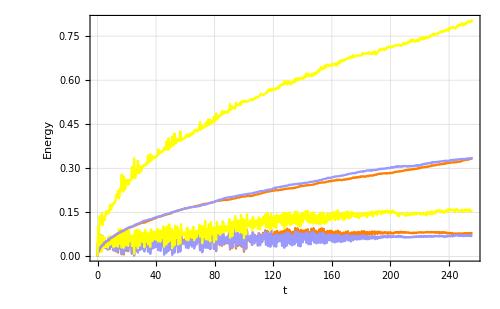

```mathematica
plot=ListPlot[{MeanHamBdata,MeanHamCdata,MeanHamEdata,DesvHamBdata,DesvHamCdata, DesvHamEdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
(*PlotRange->{{x0,x1},{y0,y1}},*)
(*PlotLegends->Placed[{"FPIEA","DP","Hairer"(*,"standard deviation"*)},Below],*)
(*PlotLabels->Placed[{"ΔE","ΔE","ΔE","σ","σ","σ"},{Scaled[1],Above}],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine,StyleHairer,StyleIdeal,StyleMachine,StyleHairer},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1,Show[plot] ];
```

#### Plot (1b) (* mean detail*)

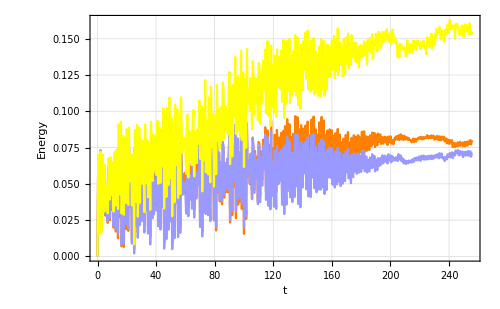

```mathematica
plot=ListPlot[{MeanHamBdata,MeanHamCdata,MeanHamEdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
(*PlotRange->{{x0,x1},{y0,y1}},*)
(*PlotLegends->Placed[{"FPIEA","DP"(*,"Hairer"*)(*,"standard deviation"*)},Below],*)
(*PlotLabels->Placed[{"ΔE","ΔE","ΔE","σ","σ","σ"},{Scaled[1],Above}],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine,StyleHairer,StyleIdeal,StyleMachine,StyleHairer},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1b,Show[plot] ];
```

#### Alpha*Sqrt[n]

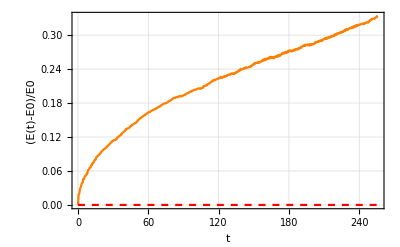

```mathematica
alphaB=2^(-55.8);
HamBdataT12=Transpose[{tpA,FunT12[alphaB,tpB]}];
plot=ListPlot[{DesvHamBdata,HamBdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

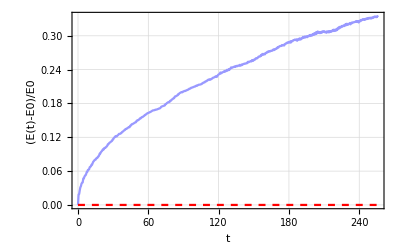

```mathematica
alphaC=2^(-55.5);
HamCdataT12=Transpose[{tpC,FunT12[alphaC,tpC]}];
plot=ListPlot[{DesvHamCdata,HamCdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{(*StyleIdeal,*)StyleMachine,(*StyleClassic,*)StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

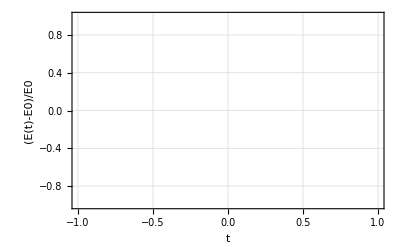

```mathematica
alphaD=2^(-54.7);
HamDdataT12=Transpose[{tpD,FunT12[alphaD,tpD]}];
plot=ListPlot[{DesvHamDdata,HamDdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{(*StyleIdeal,StyleMachine,*)StyleClassic,StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

#### Plot (2)

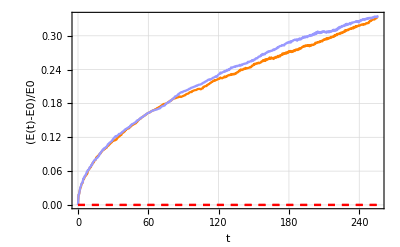

```mathematica
plot=ListPlot[{DesvHamBdata,DesvHamCdata,DesvHamDdata,
                             HamBdataT12,HamCdataT12,HamDdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic,
                       StyleHamT12,StyleHamT12,StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot2,Show[plot] ];
```

### Graphics-I (Energy-2): Plot11,Plot12,Plot13

```mathematica
maxnstat=100;
If[nstat<maxnstat,nstat0=nstat,nstat0=maxnstat];
```

```mathematica
AllHamerrB=FunAllEnergy[outB, nstat0,noutB,HAM, parameters,neq,prec,step] ;
AllHamerrC=FunAllEnergy[outC, nstat0,noutC,HAM, parameters,neq,prec,step] ;
AllHamerrD=FunAllEnergy[outD, nstat0,noutD,HAM, parameters,neq,prec,step] ;
```

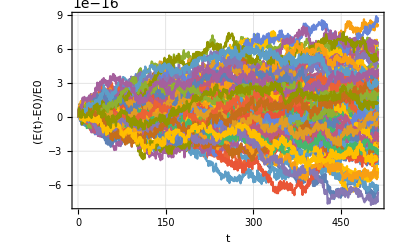

```mathematica
plot=ListPlot[Table[AllHamerrB[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot11,Show[plot] ];
```

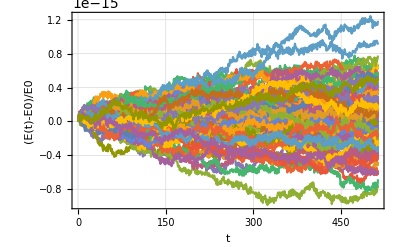

```mathematica
plot=ListPlot[Table[AllHamerrC[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot12,Show[plot] ];
```

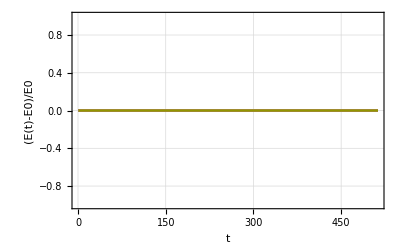

```mathematica
plot=ListPlot[Table[AllHamerrD[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot13,Show[plot] ];
```

### Graphics-II (Global Error): Plot3

```mathematica
{MeanErrA,DesvErrA}=FunErrorNEW[outA, outA,ERR, nstat,noutA,neq,prec,step];
{MeanErrB,DesvErrB}=FunErrorNEW[outA, outB,ERR, nstat,noutA,neq,prec,step];
{MeanErrC,DesvErrC}=FunErrorNEW[outA, outC,ERR, nstat,noutA,neq,prec,step];
{MeanErrD,DesvErrD}=FunErrorNEW[outA, outD,ERR, nstat,noutA,neq,prec,step];
```

```mathematica
MeanErrBdata = Transpose[{tpB,MeanErrB}];
MeanErrCdata = Transpose[{tpC,MeanErrC}];
MeanErrDdata = Transpose[{tpD,MeanErrD}];

DesvErrBdata = Transpose[{tpB,DesvErrB}];
DesvErrCdata = Transpose[{tpC,DesvErrC}];
DesvErrDdata = Transpose[{tpD,DesvErrD}];
```

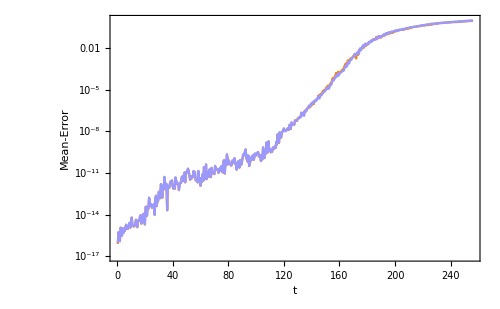

```mathematica
plot=ListLogPlot[{MeanErrBdata,MeanErrCdata},
AxesLabel->{"t","Mean-Error"},Joined->True,
PlotRange->All,
(*PlotLegends->Placed[{"FPIEA","DP"},Below],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Mean-Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot3,Show[plot] ];
```

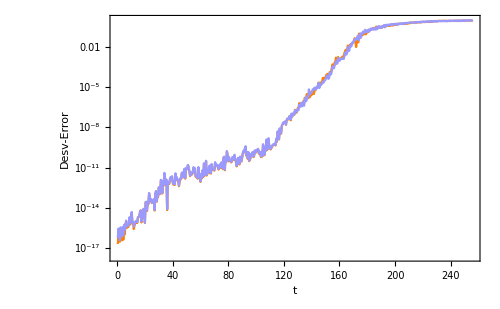

```mathematica
plot=ListLogPlot[{DesvErrBdata,DesvErrCdata},
AxesLabel->{"t","Desv-Error"},Joined->True,
PlotRange->All,
(*PlotLegends->Placed[{"FPIEA","DP"},Below],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Desv-Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot3b,Show[plot] ];
```

### Graphics-III (Histogram) : Plot4, Plot5

```mathematica
HamerrA=FunHamErrDif[outA,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrB=FunHamErrDif[outB,nstat,noutB,HAM, parameters,neq,prec,step] ;
HamerrC=FunHamErrDif[outC,nstat,noutC,HAM, parameters,neq,prec,step] ;
HamerrD=FunHamErrDif[outD,nstat,noutD,HAM, parameters,neq,prec,step] ;
```

#### B-Integration: Plot4

0.0001563153105931867397960783525639370525696249222510530868128676008734832211805681

0.03901806277589897334477830746239796038240922824996605581914268083486238533073104636

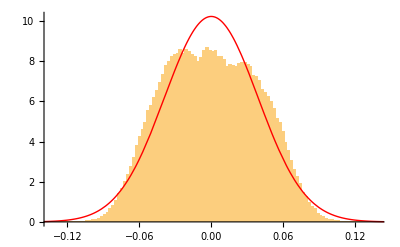

/home/mikel/1-Artikulua-Esperimentuak-4B/15-EsperimentuaV154 (artikulua)/Experiments/CDP-NEW (p=1000,approx=0)/Images/CDP2A.pdf

```mathematica
Hamerdif=HamerrB 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[plot4,Show[ir1,ir2]]
```

```mathematica
Length[Hamerdif]
```

512000

#### C-Integration: Plot5

0.0001389961013593184761626614920210516105510335231862283309478374536502759364167736

0.03915380196203915010676962565514606076671248242732702682883587009201596281714413801

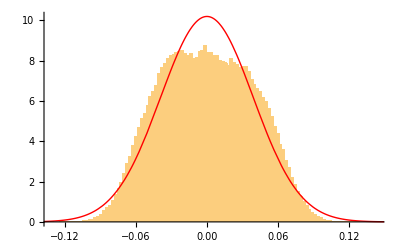

/home/mikel/1-Artikulua-Esperimentuak-4B/15-EsperimentuaV154 (artikulua)/Experiments/CDP-NEW (p=1000,approx=0)/Images/CDP2B.pdf

```mathematica
Hamerdif=HamerrC 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[plot5,Show[ir1,ir2]]
```

### Tables

#### Quadruple

```mathematica
MeanD0=0.; (*(SD0A/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamA]]//N;
Hamerdif=Drop[MeanHamA ,1]-Drop[ MeanHamA,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrA]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.85802×10^-19,3.2792×10^-22,8.45269×10^-21,0.}

#### FPIEA

```mathematica
MeanD0=0.;(*(SD0B/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamB]]//N;
Hamerdif=Drop[MeanHamB ,1]-Drop[ MeanHamB,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrB]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,9.66605×10^-17,1.56315×10^-19,2.64069×10^-17,0.908251}

#### DP

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamC]]//N;
Hamerdif=Drop[MeanHamC ,1]-Drop[ MeanHamC,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrC]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,9.20291×10^-17,1.38996×10^-19,2.6405×10^-17,0.983295}

#### DP-Estandarra

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamD]]//N;
Hamerdif=Drop[MeanHamD ,1]-Drop[ MeanHamD,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrD]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,0.,0.,0.,2.2108}

## Analisis-II: error estimation

```mathematica
Now
```

Fri 6 Jan 2017 11:18:25

### Estimation: Plot6

```mathematica
tp=tpC;
{MeanEst,DesvEst,MeanQty,DesvQty}=FunEstimation[outA,outC,ERR,nstat,noutA,neq,prec,step];
MeanEstdata = Transpose[{tp,MeanEst}];
Desvdata1=Transpose[{tp,MeanEst+DesvEst}];
Desvdata2=Transpose[{tp,MeanEst-DesvEst}];
```

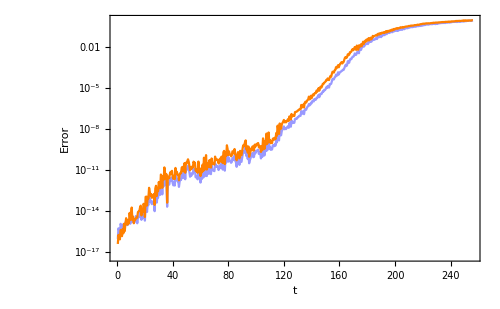

```mathematica
MeanErrdata=MeanErrCdata;
plot=ListLogPlot[{Abs[MeanErrdata ],Abs[MeanEstdata]},
AxesLabel->{"t","Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
(*PlotLegends->Placed[{"Error","Estimation"},Below],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot6,Show[plot]];
```

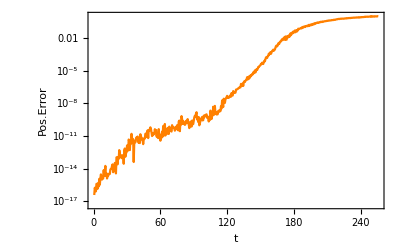

```mathematica
plot=ListLogPlot[{(*Abs[MeanErrCdata],*)Abs[MeanEstdata]},AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
```

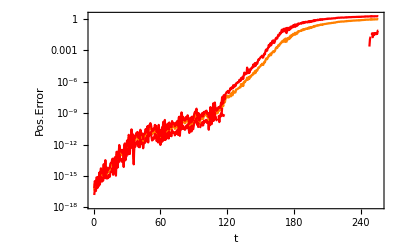

```mathematica
plot6b=ListLogPlot[{ MeanEstdata, Desvdata1,Desvdata2},
AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{Orange,Red,Red},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
```

### Estimation: Plot6a (bakarra)

```mathematica
tp=tpC;
mynstat=1;
{MeanEst,DesvEst,MeanQty,DesvQty}=FunEstimation[outA,outC,ERR,mynstat,noutA,neq,prec,step];
MeanEstdata = Transpose[{tp,MeanEst}];
Desvdata1=Transpose[{tp,MeanEst+DesvEst}];
Desvdata2=Transpose[{tp,MeanEst-DesvEst}];
```

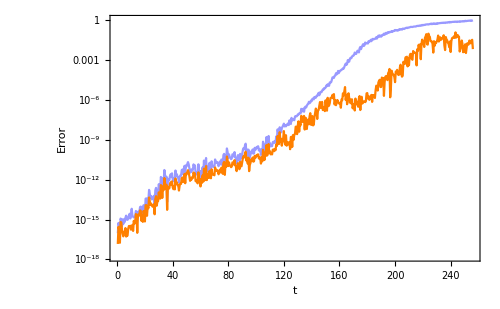

```mathematica
MeanErrdata=MeanErrCdata;
plot=ListLogPlot[{Abs[MeanErrdata ],Abs[MeanEstdata]},
AxesLabel->{"t","Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
(*PlotLegends->Placed[{"Error","Estimation"},Below],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot6a,Show[plot]];
```

### Quality estimation: Plot7

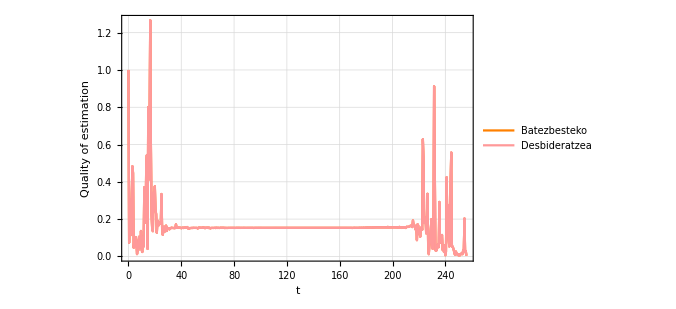

```mathematica
MeanQtydata=Transpose[{tpC,10^MeanQty}];
MeanQtyData1=Transpose[{tpC,10^(MeanQty+DesvQty)}];
MeanQtyData2=Transpose[{tpC,10^(MeanQty-DesvQty)}];
plot=ListPlot[{MeanQtydata,MeanQtyData1,MeanQtyData2},
AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotLegends->Placed[{"Batezbesteko","Desbideratzea"},Below],
PlotRange->All,
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleEstimation,Lighter[Red,.6],Lighter[Red,.6]},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Quality of estimation"},
LabelStyle->Directive[Black,Bold]
]
Export[plot7,Show[plot]];
```

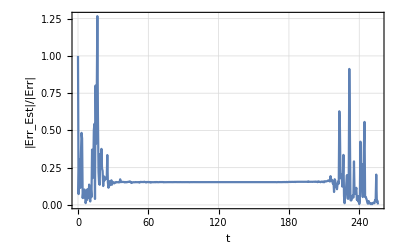

```mathematica
plot=ListPlot[{MeanQtydata},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","|Err_Est|/|Err|"}]
```